```mathematica
NormalDistribution[1,0.1]
```

NormalDistribution[1,0.1]

```mathematica
PDF[NormalDistribution[1,0.1],x]
```

3.98942 ⅇ^(-50. (-1+x)^2)

```mathematica
ParametricPlot3D[({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}}).{RandomReal[NormalDistribution[1,0.1]]Sin[u],RandomReal[NormalDistribution[1,0.1]]Cos[u],u/10},{u,0,20}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[({{Cos, 0, 0}, {0, 1, 0}, {0, 0, 1}}).{RandomReal[NormalDistribution[1,0.1]]Sin[u],RandomReal[NormalDistribution[1,0.1]]Cos[u],u/10},{u,0,20}]
```

-Graphics3D-

```mathematica
L=10; R = 2;
y0=0;
noise=0.1;
ω0=2;
ParametricPlot3D[({{Cos[ω0 z], Sin[ω0 z], 0}, {-Sin[ω0 z], Cos[ω0 z], 0}, {0, 0, 1}}).{noise RandomReal[NormalDistribution[0,0.1]],Sqrt[R^2-(z-L/2)^2]-Sqrt[(L/2)^2-R^2]+noise RandomReal[NormalDistribution[0,0.1]],z},{z,0,L},BoxStyle->Dashing[{0.02,0.02}],Axes->True,AxesStyle->Thickness[0.005]]
```

-Graphics3D-

```mathematica
L=6; R = 4;
y0=0;
noise=.1;
ω0=2;
ParametricPlot3D[({{Cos[ω0 z], Sin[ω0 z], 0}, {-Sin[ω0 z], Cos[ω0 z], 0}, {0, 0, 1}}).{noise RandomReal[NormalDistribution[0,0.1]],Sqrt[R^2-(z-L/2)^2]-Sqrt[R^2-(L/2)^2]+noise RandomReal[NormalDistribution[0,0.1]],z},{z,0,L},BoxStyle->Dashing[{0.02,0.02}],Axes->True,AxesOrigin->{0,0,0},PlotRange->All]
```

-Graphics3D-

```mathematica
({{Cos[ω0 z], Sin[ω0 z], 0}, {-Sin[ω0 z], Cos[ω0 z], 0}, {0, 0, 1}}).{a,b,c}
```

{a Cos[2 z]+b Sin[2 z],b Cos[2 z]-a Sin[2 z],c}

```mathematica
NormalDistribution[μ,σ]
```

NormalDistribution[μ,σ]

```mathematica
Σ={{Subscript[σ,1]^2,ρ Subscript[σ,1] Subscript[σ,2]},{ρ Subscript[σ,1] Subscript[σ,2],Subscript[σ,2]^2}};
```

```mathematica
MultinormalDistribution[{Subscript[μ,1],Subscript[μ,2]},Σ]
```

MultinormalDistribution[{μ_1,μ_2},{{σ_1^2,ρ σ_1 σ_2},{ρ σ_1 σ_2,σ_2^2}}]

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{{Subscript[σ, 1]^2,ρ Subscript[σ, 1] Subscript[σ, 2]},{ρ Subscript[σ, 1] Subscript[σ, 2],Subscript[σ, 2]^2}}],{x,y}]
```

(ⅇ^(1/2 (-((x-μ_1) (y ρ σ_1-ρ μ_2 σ_1-x σ_2+μ_1 σ_2))/((-1+ρ^2) σ_1^2 σ_2)-((y-μ_2) (-y σ_1+μ_2 σ_1+x ρ σ_2-ρ μ_1 σ_2))/((-1+ρ^2) σ_1 σ_2^2))))/(2 π √(σ_1^2 σ_2^2-ρ^2 σ_1^2 σ_2^2))

```mathematica
Clear[Σ]
```

```mathematica
PDF[MultinormalDistribution[{Subscript[μ, 1],Subscript[μ, 2]},{{Subscript[Σ, 11],Subscript[Σ, 12]},{Subscript[Σ, 12],Subscript[Σ, 22]}}],{x,y}]
```

(ⅇ^(1/2 (-((y-μ_2) (y Σ_11-μ_2 Σ_11-x Σ_12+μ_1 Σ_12))/(-Σ_12^2+Σ_11 Σ_22)-((x-μ_1) (-y Σ_12+μ_2 Σ_12+x Σ_22-μ_1 Σ_22))/(-Σ_12^2+Σ_11 Σ_22))))/(2 π √(-Σ_12^2+Σ_11 Σ_22))

```mathematica
Clear[y0]
```

```mathematica
Series[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,x0,2},{y,y0,2}]//Simplify
```

((ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))))/(2 π √(-Σ_12^2+Σ_11 Σ_22))+(ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) ((-y0+μ_2) Σ_11+(x0-μ_1) Σ_12) (y-y0))/(2 π (-Σ_12^2+Σ_11 Σ_22)^(3/2))+(ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (((y0-μ_2) Σ_11+(-x0+μ_1) Σ_12)^2+Σ_11 (Σ_12^2-Σ_11 Σ_22)) (y-y0)^2)/(4 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))+O[y-y0]^3)+((ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) ((y0-μ_2) Σ_12+(-x0+μ_1) Σ_22))/(2 π (-Σ_12^2+Σ_11 Σ_22)^(3/2))-1/(2 (π (-Σ_12^2+Σ_11 Σ_22)^(5/2)))(ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (Σ_12 (-((x0-μ_1) (y0-μ_2) Σ_12)+Σ_12^2+(x0-μ_1)^2 Σ_22)+Σ_11 (Σ_12 (y0^2-2 y0 μ_2+μ_2^2-Σ_22)-(x0-μ_1) (y0-μ_2) Σ_22))) (y-y0)+1/(4 π (-Σ_12^2+Σ_11 Σ_22)^(7/2))ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (2 Σ_12 ((y0-μ_2) Σ_11+(-x0+μ_1) Σ_12) (Σ_12^2-Σ_11 Σ_22)+((y0-μ_2) Σ_12+(-x0+μ_1) Σ_22) (((y0-μ_2) Σ_11+(-x0+μ_1) Σ_12)^2+Σ_11 (Σ_12^2-Σ_11 Σ_22))) (y-y0)^2+O[y-y0]^3) (x-x0)+((ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (((y0-μ_2) Σ_12+(-x0+μ_1) Σ_22)^2+Σ_22 (Σ_12^2-Σ_11 Σ_22)))/(4 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))-1/(4 (π (-Σ_12^2+Σ_11 Σ_22)^(7/2)))(ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (2 Σ_12 ((y0-μ_2) Σ_12+(-x0+μ_1) Σ_22) (Σ_12^2-Σ_11 Σ_22)+((y0-μ_2) Σ_11+(-x0+μ_1) Σ_12) (((y0-μ_2) Σ_12+(-x0+μ_1) Σ_22)^2+Σ_22 (Σ_12^2-Σ_11 Σ_22)))) (y-y0)+1/(8 π (-Σ_12^2+Σ_11 Σ_22)^(9/2))ⅇ^(((y0-μ_2)^2 Σ_11+(x0-μ_1) (-2 (y0-μ_2) Σ_12+(x0-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (4 Σ_12 ((y0-μ_2) Σ_11+(-x0+μ_1) Σ_12) ((y0-μ_2) Σ_12+(-x0+μ_1) Σ_22) (Σ_12^2-Σ_11 Σ_22)+2 (Σ_12^3-Σ_11 Σ_12 Σ_22)^2+(((y0-μ_2) Σ_11+(-x0+μ_1) Σ_12)^2+Σ_11 (Σ_12^2-Σ_11 Σ_22)) (((y0-μ_2) Σ_12+(-x0+μ_1) Σ_22)^2+Σ_22 (Σ_12^2-Σ_11 Σ_22))) (y-y0)^2+O[y-y0]^3) (x-x0)^2+O[x-x0]^3

```mathematica
Series[PDF[NormalDistribution[Subscript[μ, 1],Subscript[σ, 1]],{x}],{x,x0,2}]
```

{(ⅇ^(-(x0-μ_1)^2/(2 σ_1^2)))/(√(2 π) σ_1)+(ⅇ^(-(x0-μ_1)^2/(2 σ_1^2)) (-x0+μ_1) (x-x0))/(√(2 π) σ_1^3)+(ⅇ^(-(x0-μ_1)^2/(2 σ_1^2)) ((-x0+μ_1)^2/σ_1^4-1/σ_1^2) (x-x0)^2)/(2 √(2 π) σ_1)+O[x-x0]^3}

```mathematica
-Inverse[{{Subscript[Σ, 11],Subscript[Σ, 12]},{Subscript[Σ, 12],Subscript[Σ, 22]}}].{xm,ym}//Simplify
```

{(-ym Σ_12+xm Σ_22)/(Σ_12^2-Σ_11 Σ_22),(ym Σ_11-xm Σ_12)/(Σ_12^2-Σ_11 Σ_22)}

```mathematica
(Subscript[Σ, 12]^2-Subscript[Σ, 11] Subscript[Σ, 22])^0((ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])))^-1 D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,1}]/.{x->xm+Subscript[μ, 1],y->ym+Subscript[μ, 2]}//FullSimplify
```

(-ym Σ_12+xm Σ_22)/(Σ_12^2-Σ_11 Σ_22)

```mathematica
(Subscript[Σ, 12]^2-Subscript[Σ, 11] Subscript[Σ, 22])^2((ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])))^-1 D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,2}]/.{x->xm+Subscript[μ, 1],y->ym+Subscript[μ, 2]}//FullSimplify
(Subscript[Σ, 12]^2-Subscript[Σ, 11] Subscript[Σ, 22])^2((ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])))^-1 D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),x],y]/.{x->xm+Subscript[μ, 1],y->ym+Subscript[μ, 2]}//FullSimplify
(Subscript[Σ, 12]^2-Subscript[Σ, 11] Subscript[Σ, 22])^2((ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])))^-1 D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{y,2}]/.{x->xm+Subscript[μ, 1],y->ym+Subscript[μ, 2]}//FullSimplify
```

-2 xm ym Σ_12 Σ_22+(xm^2-Σ_11) Σ_22^2+Σ_12^2 (ym^2+Σ_22)

```mathematica
Expand[-2 xm ym Subscript[Σ, 12] Subscript[Σ, 22]+(xm^2-Subscript[Σ, 11]) Subscript[Σ, 22]^2+Subscript[Σ, 12]^2 (ym^2+Subscript[Σ, 22])]
```

ym^2 Σ_12^2-2 xm ym Σ_12 Σ_22+Σ_12^2 Σ_22+xm^2 Σ_22^2-Σ_11 Σ_22^2

```mathematica
Expand[-Subscript[Σ, 12] (-xm ym Subscript[Σ, 12]+Subscript[Σ, 12]^2+xm^2 Subscript[Σ, 22])+Subscript[Σ, 11] (xm ym Subscript[Σ, 22]+Subscript[Σ, 12] (-ym^2+Subscript[Σ, 22]))]
```

-ym^2 Σ_11 Σ_12+xm ym Σ_12^2-Σ_12^3+xm ym Σ_11 Σ_22-xm^2 Σ_12 Σ_22+Σ_11 Σ_12 Σ_22

```mathematica
Expand[xm^2 Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 12] (-2 xm ym+Subscript[Σ, 12])+Subscript[Σ, 11]^2 (ym^2-Subscript[Σ, 22])]
```

ym^2 Σ_11^2-2 xm ym Σ_11 Σ_12+xm^2 Σ_12^2+Σ_11 Σ_12^2-Σ_11^2 Σ_22

```mathematica
((ⅇ^(-(x0-Subscript[μ, 1])^2/(2 Subscript[σ, 1]^2)))/(√(2 π) Subscript[σ, 1]))^-1 Series[PDF[NormalDistribution[Subscript[μ, 1],Subscript[σ, 1]],{x}],{x,x0,2}]
```

{1+((-x0+μ_1) (x-x0))/σ_1^2+1/2 ((-x0+μ_1)^2/σ_1^4-1/σ_1^2) (x-x0)^2+O[x-x0]^3}

```mathematica
((Subscript[Σ, 12]^2-Subscript[Σ, 11] Subscript[Σ, 22])^2((ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])))^-1 D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,1}],{y,1}]/.{x->xm+Subscript[μ, 1],y->ym+Subscript[μ, 2]}//FullSimplify)//Expand
```

-ym^2 Σ_11 Σ_12+xm ym Σ_12^2-Σ_12^3+xm ym Σ_11 Σ_22-xm^2 Σ_12 Σ_22+Σ_11 Σ_12 Σ_22

```mathematica
((Subscript[Σ, 12]^2-Subscript[Σ, 11] Subscript[Σ, 22])^2((ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])))^-1{{D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,2}],{y,0}],D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,1}],{y,1}]},{D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,1}],{y,1}],D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,0}],{y,2}]}}/.{x->xm+Subscript[μ, 1],y->ym+Subscript[μ, 2]}//FullSimplify)//Expand//MatrixForm
```

(ym^2 Σ_12^2-2 xm ym Σ_12 Σ_22+Σ_12^2 Σ_22+xm^2 Σ_22^2-Σ_11 Σ_22^2 | -ym^2 Σ_11 Σ_12+xm ym Σ_12^2-Σ_12^3+xm ym Σ_11 Σ_22-xm^2 Σ_12 Σ_22+Σ_11 Σ_12 Σ_22
-ym^2 Σ_11 Σ_12+xm ym Σ_12^2-Σ_12^3+xm ym Σ_11 Σ_22-xm^2 Σ_12 Σ_22+Σ_11 Σ_12 Σ_22 | ym^2 Σ_11^2-2 xm ym Σ_11 Σ_12+xm^2 Σ_12^2+Σ_11 Σ_12^2-Σ_11^2 Σ_22)

```mathematica
(Subscript[Σ, 12]^2-Subscript[Σ, 11] Subscript[Σ, 22])^2{xm,ym}.MatrixPower[{{Subscript[Σ, 11],Subscript[Σ, 12]},{Subscript[Σ, 12],Subscript[Σ, 22]}},-2].{xm,ym}//Simplify//Expand
```

ym^2 Σ_11^2-2 xm ym Σ_11 Σ_12+xm^2 Σ_12^2+ym^2 Σ_12^2-2 xm ym Σ_12 Σ_22+xm^2 Σ_22^2

```mathematica
Hf=({{D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,2}],{y,0}],D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,1}],{y,1}]},{D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,1}],{y,1}],D[D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])),{x,0}],{y,2}]}}//Simplify)
```

{{(ⅇ^(((y-μ_2)^2 Σ_11+(x-μ_1) (-2 (y-μ_2) Σ_12+(x-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (-2 (x-μ_1) (y-μ_2) Σ_12 Σ_22+(x^2-2 x μ_1+μ_1^2-Σ_11) Σ_22^2+Σ_12^2 (y^2-2 y μ_2+μ_2^2+Σ_22)))/(2 π (-Σ_12^2+Σ_11 Σ_22)^(5/2)),-1/(2 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))ⅇ^(((y-μ_2)^2 Σ_11+(x-μ_1) (-2 (y-μ_2) Σ_12+(x-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (Σ_12 (-((x-μ_1) (y-μ_2) Σ_12)+Σ_12^2+(x-μ_1)^2 Σ_22)+Σ_11 (Σ_12 (y^2-2 y μ_2+μ_2^2-Σ_22)-(x-μ_1) (y-μ_2) Σ_22))},{-1/(2 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))ⅇ^(((y-μ_2)^2 Σ_11+(x-μ_1) (-2 (y-μ_2) Σ_12+(x-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) (Σ_12 (-((x-μ_1) (y-μ_2) Σ_12)+Σ_12^2+(x-μ_1)^2 Σ_22)+Σ_11 (Σ_12 (y^2-2 y μ_2+μ_2^2-Σ_22)-(x-μ_1) (y-μ_2) Σ_22)),(ⅇ^(((y-μ_2)^2 Σ_11+(x-μ_1) (-2 (y-μ_2) Σ_12+(x-μ_1) Σ_22))/(2 (Σ_12^2-Σ_11 Σ_22))) ((x-μ_1)^2 Σ_12^2+Σ_11 Σ_12 (-2 x y+2 μ_1 (y-μ_2)+2 x μ_2+Σ_12)+Σ_11^2 (y^2-2 y μ_2+μ_2^2-Σ_22)))/(2 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))}}

```mathematica
Exp1=D[((ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))/.{x->x0,y->y0}){x0-Subscript[μ, 1],y0-Subscript[μ, 2]}.MatrixPower[{{Subscript[Σ, 11],Subscript[Σ, 12]},{Subscript[Σ, 12],Subscript[Σ, 22]}},-1]/.{Subscript[μ, 1]->Subscript[μ, 1][z],Subscript[μ, 2]->Subscript[μ, 2][z]},z]//Simplify
Exp2={D[(D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))/.{Subscript[μ, 1]->Subscript[μ, 1][z],Subscript[μ, 2]->Subscript[μ, 2][z]},z]),x]/.{x->x0,y->y0},D[(D[(ⅇ^(1/2 (-((y-Subscript[μ, 2]) (y Subscript[Σ, 11]-Subscript[μ, 2] Subscript[Σ, 11]-x Subscript[Σ, 12]+Subscript[μ, 1] Subscript[Σ, 12]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22])-((x-Subscript[μ, 1]) (-y Subscript[Σ, 12]+Subscript[μ, 2] Subscript[Σ, 12]+x Subscript[Σ, 22]-Subscript[μ, 1] Subscript[Σ, 22]))/(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))))/(2 π √(-Subscript[Σ, 12]^2+Subscript[Σ, 11] Subscript[Σ, 22]))/.{Subscript[μ, 1]->Subscript[μ, 1][z],Subscript[μ, 2]->Subscript[μ, 2][z]},z]),y]/.{x->x0,y->y0}}//Simplify
Exp1/Exp2//Simplify
```

{1/(2 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))ⅇ^(((x0-μ_1[z]) (Σ_22 (x0-μ_1[z])-2 Σ_12 (y0-μ_2[z]))+Σ_11 (y0-μ_2[z])^2)/(2 (Σ_12^2-Σ_11 Σ_22))) (-Σ_12^3 μ_2'[z]+Σ_12^2 ((Σ_22+(y0-μ_2[z])^2) μ_1'[z]+(x0-μ_1[z]) (y0-μ_2[z]) μ_2'[z])+Σ_22 (Σ_22 (-Σ_11+(x0-μ_1[z])^2) μ_1'[z]+Σ_11 (x0-μ_1[z]) (y0-μ_2[z]) μ_2'[z])-Σ_12 (Σ_11 (y0-μ_2[z])^2 μ_2'[z]+Σ_22 (2 (x0-μ_1[z]) (y0-μ_2[z]) μ_1'[z]+(-Σ_11+(x0-μ_1[z])^2) μ_2'[z]))),1/(2 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))ⅇ^(((x0-μ_1[z]) (Σ_22 (x0-μ_1[z])-2 Σ_12 (y0-μ_2[z]))+Σ_11 (y0-μ_2[z])^2)/(2 (Σ_12^2-Σ_11 Σ_22))) (Σ_11^2 (-Σ_22+(y0-μ_2[z])^2) μ_2'[z]-Σ_12 (Σ_12^2 μ_1'[z]+Σ_22 (x0-μ_1[z])^2 μ_1'[z]-Σ_12 (x0-μ_1[z]) ((y0-μ_2[z]) μ_1'[z]+(x0-μ_1[z]) μ_2'[z]))+Σ_11 (Σ_22 (x0-μ_1[z]) (y0-μ_2[z]) μ_1'[z]+Σ_12^2 μ_2'[z]+Σ_12 (-((-Σ_22+(y0-μ_2[z])^2) μ_1'[z])-2 (x0-μ_1[z]) (y0-μ_2[z]) μ_2'[z])))}

{1/(2 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))ⅇ^(((x0-μ_1[z]) (Σ_22 (x0-μ_1[z])-2 Σ_12 (y0-μ_2[z]))+Σ_11 (y0-μ_2[z])^2)/(2 (Σ_12^2-Σ_11 Σ_22))) (Σ_12^3 μ_2'[z]-Σ_12^2 ((Σ_22+(y0-μ_2[z])^2) μ_1'[z]+(x0-μ_1[z]) (y0-μ_2[z]) μ_2'[z])+Σ_22 (-Σ_22 (-Σ_11+(x0-μ_1[z])^2) μ_1'[z]-Σ_11 (x0-μ_1[z]) (y0-μ_2[z]) μ_2'[z])+Σ_12 (Σ_11 (y0-μ_2[z])^2 μ_2'[z]+Σ_22 (2 (x0-μ_1[z]) (y0-μ_2[z]) μ_1'[z]+(-Σ_11+(x0-μ_1[z])^2) μ_2'[z]))),1/(2 π (-Σ_12^2+Σ_11 Σ_22)^(5/2))ⅇ^(((x0-μ_1[z]) (Σ_22 (x0-μ_1[z])-2 Σ_12 (y0-μ_2[z]))+Σ_11 (y0-μ_2[z])^2)/(2 (Σ_12^2-Σ_11 Σ_22))) (-Σ_11^2 (-Σ_22+(y0-μ_2[z])^2) μ_2'[z]+Σ_12 (Σ_12^2 μ_1'[z]+Σ_22 (x0-μ_1[z])^2 μ_1'[z]-Σ_12 (x0-μ_1[z]) ((y0-μ_2[z]) μ_1'[z]+(x0-μ_1[z]) μ_2'[z]))+Σ_11 (-Σ_22 (x0-μ_1[z]) (y0-μ_2[z]) μ_1'[z]-Σ_12^2 μ_2'[z]+Σ_12 ((-Σ_22+(y0-μ_2[z])^2) μ_1'[z]+2 (x0-μ_1[z]) (y0-μ_2[z]) μ_2'[z])))}

{-1,-1}

```mathematica
({{Cos[ω0 z], Sin[ω0 z], 0}, {-Sin[ω0 z], Cos[ω0 z], 0}, {0, 0, 1}}).{σ Subscript[η, x],Sqrt[R^2-(z-L/2)^2]-Sqrt[R^2-(L/2)^2]+σ Subscript[η, y],z}
```

{σ Cos[z ω0] η_x+Sin[z ω0] (-√(-L^2/4+R^2)+√(R^2-(-L/2+z)^2)+σ η_y),-σ Sin[z ω0] η_x+Cos[z ω0] (-√(-L^2/4+R^2)+√(R^2-(-L/2+z)^2)+σ η_y),z}

```mathematica
Bx=σ Cos[z ω0] η1+Sin[z ω0] (-√(-L^2/4+R^2)+√(R^2-(-L/2+z)^2)+σ η2);
By=-σ Sin[z ω0] η1+Cos[z ω0] (-√(-L^2/4+R^2)+√(R^2-(-L/2+z)^2)+σ η2);
```

```mathematica
f[z_]=PDF[MultinormalDistribution[{M1,M2},{{Subscript[Σ, 11],Subscript[Σ, 12]},{Subscript[Σ, 12],Subscript[Σ, 22]}}],{x,y}]/.{M1->Bx,M2->By}//Cancel
```

1/(2 π √(-Σ_12^2+Σ_11 Σ_22))ⅇ^(-((y-(-1/2 √(-L^2+4 R^2)+1/2 √(-L^2+4 R^2+4 L z-4 z^2)+η2 σ) Cos[z ω0]+η1 σ Sin[z ω0]) (y Σ_11-((-1/2 √(-L^2+4 R^2)+1/2 √(-L^2+4 R^2+4 L z-4 z^2)+η2 σ) Cos[z ω0]-η1 σ Sin[z ω0]) Σ_11-x Σ_12+(η1 σ Cos[z ω0]+(-1/2 √(-L^2+4 R^2)+1/2 √(-L^2+4 R^2+4 L z-4 z^2)+η2 σ) Sin[z ω0]) Σ_12))/(2 (-Σ_12^2+Σ_11 Σ_22))-((x-η1 σ Cos[z ω0]-(-1/2 √(-L^2+4 R^2)+1/2 √(-L^2+4 R^2+4 L z-4 z^2)+η2 σ) Sin[z ω0]) (-y Σ_12+((-1/2 √(-L^2+4 R^2)+1/2 √(-L^2+4 R^2+4 L z-4 z^2)+η2 σ) Cos[z ω0]-η1 σ Sin[z ω0]) Σ_12+x Σ_22-(η1 σ Cos[z ω0]+(-1/2 √(-L^2+4 R^2)+1/2 √(-L^2+4 R^2+4 L z-4 z^2)+η2 σ) Sin[z ω0]) Σ_22))/(2 (-Σ_12^2+Σ_11 Σ_22)))

```mathematica
out=(MatrixPower[Hf,-1]/.{x->x0,y->y0,Subscript[μ, 1]->Bx,Subscript[μ, 2]->By}).(-{D[D[f[z],z],x],D[D[f[z],z],y]}/.{x->x0,y->y0});
```

```mathematica
out//Simplify
```

{1/(2 √(-L^2+4 R^2+4 L z-4 z^2))(-((L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)-2 √(-L^2+4 R^2+4 L z-4 z^2) η2 σ) ω0 Cos[z ω0])+2 (L-2 z-√(-L^2+4 R^2+4 L z-4 z^2) η1 σ ω0) Sin[z ω0]),1/(2 √(-L^2+4 R^2+4 L z-4 z^2))(2 (L-2 z-√(-L^2+4 R^2+4 L z-4 z^2) η1 σ ω0) Cos[z ω0]+(L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)-2 √(-L^2+4 R^2+4 L z-4 z^2) η2 σ) ω0 Sin[z ω0])}

```mathematica
nonoiseout={1/(2 √(-L^2+4 R^2+4 L z-4 z^2))(-((L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)-2 √(-L^2+4 R^2+4 L z-4 z^2) η2 σ) ω0 Cos[z ω0])+2 (L-2 z-√(-L^2+4 R^2+4 L z-4 z^2) η1 σ ω0) Sin[z ω0]),1/(2 √(-L^2+4 R^2+4 L z-4 z^2))(2 (L-2 z-√(-L^2+4 R^2+4 L z-4 z^2) η1 σ ω0) Cos[z ω0]+(L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)-2 √(-L^2+4 R^2+4 L z-4 z^2) η2 σ) ω0 Sin[z ω0])}/.{σ->0}
```

{(-((L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-L^2+4 R^2+4 L z-4 z^2)),(2 (L-2 z) Cos[z ω0]+(L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0 Sin[z ω0])/(2 √(-L^2+4 R^2+4 L z-4 z^2))}

-1+R (1/(L+2 R-2 z)+1/(-L+2 (R+z)))+2 R^2 ω0^2-1/2 (L^2-2 L z+2 z^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0^2

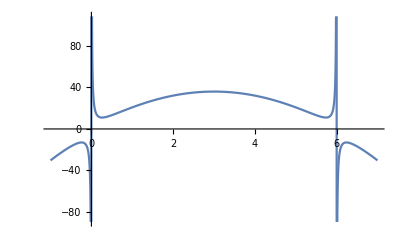

```mathematica
nonoiseout.nonoiseout//FullSimplify
Plot[%/.{L->6,R->3,ω0->2},{z,-1,7}]
```

```mathematica
ToPolarCoordinates[nonoiseout]//FullSimplify
```

{1/2 √(-4-2 (L^2-2 L z+2 z^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0^2+8 R^2 (-2/(L^2-4 R^2-4 L z+4 z^2)+ω0^2)),ArcTan[(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z))))),(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z)))))]}

```mathematica
Series[ArcTan[(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z))))),(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z)))))],{R,Infinity,2}]
```

-ⅈ Log[-(ⅇ^(-ⅈ z ω0) (-ⅈ L+2 ⅈ z-L z ω0+z^2 ω0))/(R √((L^2-4 L z+4 z^2+L^2 z^2 ω0^2-2 L z^3 ω0^2+z^4 ω0^2)/R^2))]-((L-2 z) (L-z)^2 z^2 ω0)/(4 (L^2-4 L z+4 z^2+L^2 z^2 ω0^2-2 L z^3 ω0^2+z^4 ω0^2) R^2)+O[1/R]^3

```mathematica
(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z)))))/((2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z))))))//FullSimplify
```

(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])

```mathematica
Series[ArcTan[(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])],{z,0,1}]//Simplify
```

2 ω0 z+O[z]^2

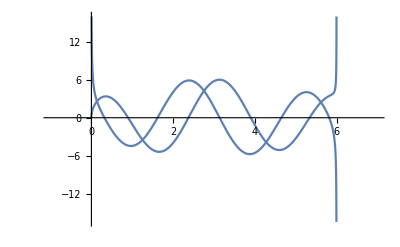

```mathematica
Plot[nonoiseout/.{L->6,R->3,ω0->2},{z,-1,7}]
```

```mathematica
nonoiseout
```

{(-((L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-L^2+4 R^2+4 L z-4 z^2)),(2 (L-2 z) Cos[z ω0]+(L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0 Sin[z ω0])/(2 √(-L^2+4 R^2+4 L z-4 z^2))}

```mathematica
ParametricPlot3D[{(-((L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-L^2+4 R^2+4 L z-4 z^2)),(2 (L-2 z) Cos[z ω0]+(L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0 Sin[z ω0])/(2 √(-L^2+4 R^2+4 L z-4 z^2)),z}/.{L->6,R->3,ω0->2},{z,0.1,6-0.1}]
```

-Graphics3D-

```mathematica
(**)
Show[ParametricPlot3D[({{Cos[ω0 z], Sin[ω0 z], 0}, {-Sin[ω0 z], Cos[ω0 z], 0}, {0, 0, 1}}).{noise RandomReal[NormalDistribution[0,0.1]],Sqrt[R^2-(z-L/2)^2]-Sqrt[R^2-(L/2)^2]+noise RandomReal[NormalDistribution[0,0.1]],z}/.{noise->0,L->6,R->3,ω0->2},{z,0,6},BoxStyle->Dashing[{0.02,0.02}],Axes->True,AxesOrigin->{0,0,0},PlotRange->All,PlotStyle->Red],ParametricPlot3D[{(-((L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-L^2+4 R^2+4 L z-4 z^2)),(2 (L-2 z) Cos[z ω0]+(L^2-4 R^2-4 L z+4 z^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0 Sin[z ω0])/(2 √(-L^2+4 R^2+4 L z-4 z^2)),z}/.{L->6,R->3,ω0->2},{z,0.01,6-0.01},PlotStyle->Green]]
```

-Graphics3D-

```mathematica
Series[ArcTan[(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])],{z,L/2,1}]//Simplify
```

-ArcTan[Cot[(L ω0)/2]]+((2+2 R^2 ω0^2-√(R^2) √(-L^2+4 R^2) ω0^2) (z-L/2))/(2 R^2 ω0-√(R^2) √(-L^2+4 R^2) ω0)+O[z-L/2]^2

```mathematica
(L ω0)/2-π/2+((2+2 R^2 ω0^2-√(R^2) √(-L^2+4 R^2) ω0^2) (z-L/2))/(2 R^2 ω0-√(R^2) √(-L^2+4 R^2) ω0)
```

```mathematica
-π/2+(L ω0)/2+((-L/2+z) (2+2 R^2 ω0^2-√(R^2) √(-L^2+4 R^2) ω0^2))/(2 R^2 ω0-√(R^2) √(-L^2+4 R^2) ω0)
```

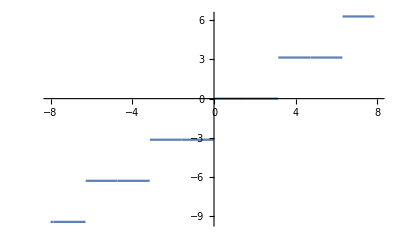

```mathematica
Plot[ArcTan[Cot[x]]-π/2+x,{x,-8,8}]
```

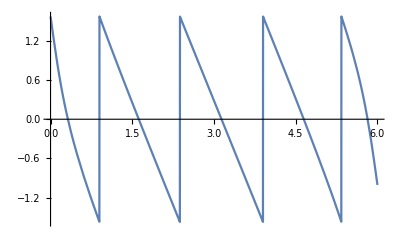

```mathematica
Plot[ArcTan[(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z)))))/((-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z))))))]/.{L->6,R->3,ω0->2},{z,0,6}]
```

```mathematica
NIntegrate[1/L D[ArcTan[(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z))))),(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z)))))],z]/.{L->10,R->8,ω0->2},{z,0,6}]
```

-1.3608

```mathematica
1/L((ArcTan[(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z))))),(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z)))))]/.{z->L})-(ArcTan[(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z))))),(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z)))))]/.{z->0}))//FullSimplify
```

(-ArcTan[0,L/(√(-L^2+4 R^2))]+ArcTan[-(L Sin[L ω0])/(√(-L^2+4 R^2)),-(L Cos[L ω0])/(√(-L^2+4 R^2))])/L

```mathematica
$Assumptions=_Symbol∈Reals
```

_Symbol∈ℝ

```mathematica
Simplify[Series[(-ArcTan[0,L/(√(-L^2+4 R^2))]+ArcTan[-(L Sin[L ω0])/(√(-L^2+4 R^2)),-(L Cos[L ω0])/(√(-L^2+4 R^2))])/L,{L,0,5}]//Normal,{L>0,R>0}]
```

-(π+2 L ω0+2 ArcTan[0,1/(√(-L^2+4 R^2))])/(2 L)

```mathematica
Series[-(π+2 L ω0+2 ArcTan[0,1/(√(-L^2+4 R^2))])/(2 L),{L,0,10}]
```

-π/L-ω0+O[L]^11

```mathematica
D[ArcTan[(-((-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Cos[z ω0])+2 (L-2 z) Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z))))),(2 (L-2 z) Cos[z ω0]+(-4 R^2+(L-2 z)^2+√(-L^2+4 R^2) √(-((L+2 R-2 z) (L-2 (R+z))))) ω0 Sin[z ω0])/(2 √(-((L+2 R-2 z) (L-2 (R+z)))))],z]//Simplify
```

(ω0 (16 R^4 (√(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2-(L-2 z)^2 (4 √(-L^2+4 R^2+4 L z-4 z^2)+2 L z (2 √(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+2 z^2 (-2 √(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L^2 (-√(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2)-8 R^2 (-√(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)+z^2 (4 √(-L^2+4 R^2)-3 √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L^2 (√(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L z (-4 √(-L^2+4 R^2)+3 √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2)))/(√(-L^2+4 R^2+4 L z-4 z^2) (L^4 ω0^2-6 L^3 z ω0^2+8 z^4 ω0^2+4 R^2 (4 R^2-√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+4 z^2 (2-6 R^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)-4 L z (2-6 R^2 ω0^2+4 z^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)+L^2 (2-8 R^2 ω0^2+14 z^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)))

```mathematica
Series[(ω0 (16 R^4 (√(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2-(L-2 z)^2 (4 √(-L^2+4 R^2+4 L z-4 z^2)+2 L z (2 √(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+2 z^2 (-2 √(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L^2 (-√(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2)-8 R^2 (-√(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)+z^2 (4 √(-L^2+4 R^2)-3 √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L^2 (√(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L z (-4 √(-L^2+4 R^2)+3 √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2)))/(√(-L^2+4 R^2+4 L z-4 z^2) (L^4 ω0^2-6 L^3 z ω0^2+8 z^4 ω0^2+4 R^2 (4 R^2-√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+4 z^2 (2-6 R^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)-4 L z (2-6 R^2 ω0^2+4 z^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)+L^2 (2-8 R^2 ω0^2+14 z^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2))),{z,L/2,2}]//FullSimplify
```

-(4+(2 √(-L^2+4 R^2))/(√(R^2))+L^2 ω0^2)/(L^2 ω0)+1/(L^6 (R^2)^(3/2) ω0^3)(128 (2 (R^2)^(3/2)+R^2 √(-L^2+4 R^2))-3 L^4 √(-L^2+4 R^2) ω0^2-8 L^2 (6 √(R^2)+√(-L^2+4 R^2)+3 (2 (R^2)^(3/2)+R^2 √(-L^2+4 R^2)) ω0^2)) (z-L/2)^2+O[z-L/2]^3

```mathematica
1/L Integrate[-ω0-1/(ω0 z^2)-(L-ⅈ √(-L^2+4 R^2))/(ω0 z^3)+(1/ω0^3+(3 ⅈ L (ⅈ L+√(-L^2+4 R^2)))/(2 ω0))/z^4+O[1/z]^5,{z,0,L}]//Normal
```

(∫_0^L ((1/ω0^3+(3 ⅈ L (ⅈ L+√(-L^2+4 R^2)))/(2 ω0))/z^4-(L-ⅈ √(-L^2+4 R^2))/(z^3 ω0)-1/(z^2 ω0)-ω0)ⅆz)/L

```mathematica
Series[1/L Integrate[ω0 (-1-1/(1+z^2 ω0^2)),{z,0,L}]//Normal,{L,Infinity,4}]//Simplify
```

-ω0-(π ω0)/(2 √(ω0^2) L)+1/(ω0 L^2)-1/(3 ω0^3 L^4)+O[1/L]^5

```mathematica
1/L Integrate[ω0 (-1-1/(1+z^2 ω0^2))+(8 R^2 z ω0)/((1+z^2 ω0^2)^2 L^3)+(16 R^2 z^2 ω0 (3+z^2 ω0^2))/((1+z^2 ω0^2)^2 L^4)+(32 R^2 z ω0 (R^2+6 z^2+3 z^4 ω0^2))/((1+z^2 ω0^2)^2 L^5),{z,0,L}]//Normal
```

(ω0 (-L^6+(68 L^4 R^2+16 L^2 R^4)/(1+L^2 ω0^2)-(L^5 ArcTan[L ω0])/ω0))/L^6

```mathematica
Series[(ω0 (-L^6+(68 L^4 R^2+16 L^2 R^4)/(1+L^2 ω0^2)-(L^5 ArcTan[L ω0])/ω0))/L^6,{L,Infinity,4}]//Simplify
```

-ω0-(π ω0)/(2 √(ω0^2) L)+1/(ω0 L^2)+(-1/(3 ω0^3)+(68 R^2)/ω0)/L^4+O[1/L]^5

```mathematica
Simplify[(ω0 (-L^2+(20 R^2)/(1+L^2 ω0^2)-(L ArcTan[L ω0])/ω0))/L^2]
```

ω0 (-1+(20 R^2)/(L^2+L^4 ω0^2))-ArcTan[L ω0]/L

```mathematica
Series[(ω0 (16 R^4 (√(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2-(L-2 z)^2 (4 √(-L^2+4 R^2+4 L z-4 z^2)+2 L z (2 √(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+2 z^2 (-2 √(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L^2 (-√(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2)-8 R^2 (-√(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)+z^2 (4 √(-L^2+4 R^2)-3 √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L^2 (√(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L z (-4 √(-L^2+4 R^2)+3 √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2)))/(√(-L^2+4 R^2+4 L z-4 z^2) (L^4 ω0^2-6 L^3 z ω0^2+8 z^4 ω0^2+4 R^2 (4 R^2-√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+4 z^2 (2-6 R^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)-4 L z (2-6 R^2 ω0^2+4 z^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)+L^2 (2-8 R^2 ω0^2+14 z^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2))),{z,L/2,2}]//FullSimplify
```

-(4+(2 √(-L^2+4 R^2))/(√(R^2))+L^2 ω0^2)/(L^2 ω0)+1/(L^6 (R^2)^(3/2) ω0^3)(128 (2 (R^2)^(3/2)+R^2 √(-L^2+4 R^2))-3 L^4 √(-L^2+4 R^2) ω0^2-8 L^2 (6 √(R^2)+√(-L^2+4 R^2)+3 (2 (R^2)^(3/2)+R^2 √(-L^2+4 R^2)) ω0^2)) (z-L/2)^2+O[z-L/2]^3

```mathematica
Series[-(4+(2 √(-L^2+4 R^2))/(√(R^2))+L^2 ω0^2)/(L^2 ω0),{L,Infinity,5} ]
```

-ω0-(2 ⅈ)/(√(R^2) ω0 L)-4/(ω0 L^2)+(4 ⅈ √(R^2))/(ω0 L^3)+(4 ⅈ R^4)/(√(R^2) ω0 L^5)+O[1/L]^6

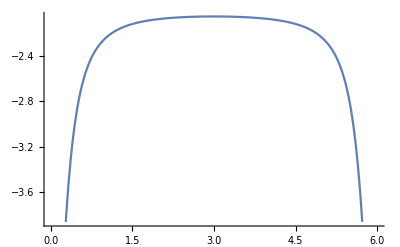

```mathematica
Plot[(ω0 (16 R^4 (√(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2-(L-2 z)^2 (4 √(-L^2+4 R^2+4 L z-4 z^2)+2 L z (2 √(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+2 z^2 (-2 √(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L^2 (-√(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2)-8 R^2 (-√(-L^2+4 R^2)+√(-L^2+4 R^2+4 L z-4 z^2)+z^2 (4 √(-L^2+4 R^2)-3 √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L^2 (√(-L^2+4 R^2)-√(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+L z (-4 √(-L^2+4 R^2)+3 √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2)))/(√(-L^2+4 R^2+4 L z-4 z^2) (L^4 ω0^2-6 L^3 z ω0^2+8 z^4 ω0^2+4 R^2 (4 R^2-√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2)) ω0^2+4 z^2 (2-6 R^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)-4 L z (2-6 R^2 ω0^2+4 z^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)+L^2 (2-8 R^2 ω0^2+14 z^2 ω0^2+√(-L^2+4 R^2) √(-L^2+4 R^2+4 L z-4 z^2) ω0^2)))/.{L->6,R->3,ω0->2},{z,0,6}]
```